{9.31322×10^-10,5.34579×10^-7,7.61449×10^-6,0.00117177,1.,1.,11642.5,1.}

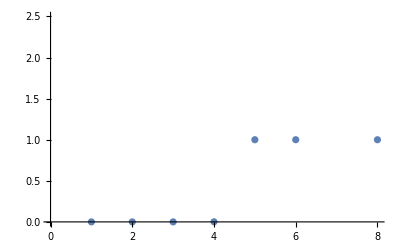

```mathematica
(* Michael Barile 
HW#1 
September 6, 2017 
MATH 68500 *)

(*Problem #1*)
f[x_,y_]:=((x+y)^2-2*x*y-y^2)/x^2;
faberr={};
For[i=1,i≤8,++i,
AppendTo[faberr,Abs[1-f[10.0^(-i),10^3]]]
;]
Print[faberr];
ListPlot[faberr]
```

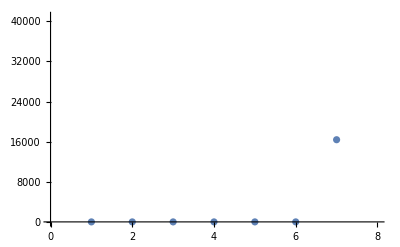

{0.,0.,0.,0.,1.,1.,16385.,2.09715×10^6}

```mathematica
(*Problem #2*)
g[x_,y_]:=(x+y)^2/x^2-2*x*y/x^2-y^2/x^2;
gaberr={};
For[i=1,i≤8,++i,
AppendTo[gaberr,Abs[1-g[10.0^(-i),10^3]]]
;]
Print[gaberr];
ListPlot[gaberr]
```

```mathematica
(* Using FullForm function to show how Mathematica interprets two mathematically
equivalent functions differently, we see why the results are different as a result of truncation error *)
FullForm[(a+b)/c]
```

Times[Plus[a,b],Power[c,-1]]

```mathematica
FullForm[a/c+b/c]
```

Plus[Times[a,Power[c,-1]],Times[b,Power[c,-1]]]

{0,0,0,0,0,0,0,0}

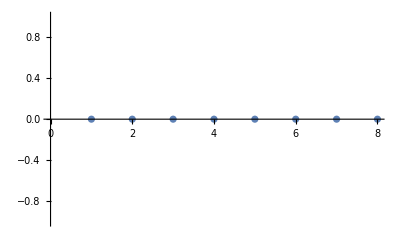

{0,0,0,0,0,0,0,0}

```mathematica
(* Problem #3 *)
(* For this problem, we use 10^(-i), which has Type Rational, as opposed to 10.0^(-i), which has Type Real, hence the different results. *)
f[x_,y_]:=((x+y)^2-2*x*y-y^2)/x^2;
faberrint={};
For[i=1,i≤8,++i,
AppendTo[faberrint,Abs[1-f[10^(-i),10^3]]] 
;]
Print[faberrint];
ListPlot[faberrint]
```

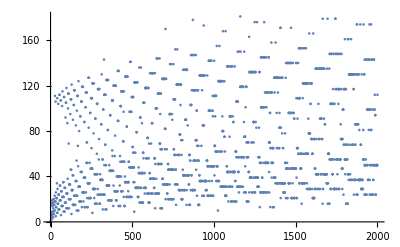

```mathematica
(*Problem #4 Collatz Conjecture *)
(* Using EvenQ function *)
list1 = {};
For[i=1,i≤2000,++i,
n=i;
count=0;
While[n≠1,
If[EvenQ[n]==True,
n=n/2;
++count,
n=3*n+1;
++count
];
];
AppendTo[list1,count]
];
ListPlot[list1]
```

```mathematica
(* Using Mod function *)
list2 = {};
For[i=1,i≤2000,++i,
n=i;
count=0;
While[n≠1,
If[Mod[n,2]==0,
n=n/2;
++count,
n=3*n+1;
++count
];
];
AppendTo[list2,count]
];
ListPlot[list2]
```

-Graphics-

```mathematica
list1==list2
```

True

```mathematica
(* Problem 1.3.1 with Newton's Method *)
f[x_]:=x^2;
fprime[x_]=D[f[x],x];
xnew=0.5;
thresh=10^-5;
iterlimit=10000;
itercnt=0;
While[Abs[f[xnew]]≥thresh && itercnt<iterlimit,
xnew=xnew-f[xnew]/fprime[xnew];
++itercnt
];
Print[xnew]
Print[itercnt]
```

0.00195313

8

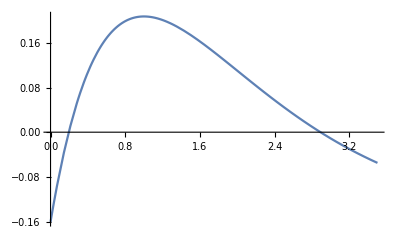

{x→2.88976}

```mathematica
(* Problem 1.3.2 with Newton's Method *)
g[x_]:=x*Exp[-x]-0.16064;
gprime[x_]=D[g[x],x];
Plot[g[x],{x,0,3.5}]
(* part a *)
FindRoot[g[x]==0,{x,3}]
```

```mathematica
(* part b *)
xnew=3;
thresh=10^-5;
iterlimit=100;
itercnt=0;
While[Abs[g[xnew]]≥thresh&&itercnt<iterlimit,
xnew=xnew-g[xnew]/gprime[xnew];
++itercnt
];
Print[xnew]
Print[itercnt]
```

2.88976

2

```mathematica
(* part c *)
xnew=3;
thresh=10^-2;
iterlimit=100;
itercnt=0;
While[Abs[g[xnew]]≥thresh&&itercnt<iterlimit,
xnew=xnew-g[xnew]/gprime[xnew];
++itercnt
];
Print[xnew]
Print[itercnt]
absrelerror=Abs[2.88976-xnew]/Abs[2.88976]
```

2.88673

1

0.00104864

```mathematica
(* Problem 1.3.1 with Midpoint Method and x^3 (instead of x^2), and with initial points
x1=-0.3, x2=0.5 *)
h[x_]:=x^3;
x1=-.3;
x2=.5;
thresh=10^-5;
iterlimit=10000;
itercnt=0;
While[Abs[h[(x1+x2)/2]]≥thresh && itercnt<iterlimit,
If[h[x1]*h[(x1+x2)/2]>=0,
x1=(x1+x2)/2;
++itercnt,
x2=(x1+x2)/2;
++itercnt
];
];
Print[N[(x1+x2)/2,6]]
Print[itercnt]
```

6.93889×10^-18

2

```mathematica
(* Problem 1.3.2 with Midpoint Method with x1=2 and x2=4 *)
(* part b *)
x1=2;
x2=4;
thresh=10^-5;
iterlimit=100;
itercnt=0;
While[Abs[g[(x1+x2)/2]]≥thresh && itercnt<iterlimit,
If[g[x1]*g[(x1+x2)/2]>=0,
x1=(x1+x2)/2;
++itercnt,
x2=(x1+x2)/2;
++itercnt
];
];
Print[N[(x1+x2)/2,6]]
Print[itercnt]
```

2.88977

13

```mathematica
(* part c *)
x1=2;
x2=4;
thresh=10^-2;
iterlimit=100;
itercnt=0;
While[Abs[g[(x1+x2)/2]]≥thresh && itercnt<iterlimit,
If[g[x1]*g[(x1+x2)/2]>=0,
x1=(x1+x2)/2;
++itercnt,
x2=(x1+x2)/2;
++itercnt
];
];
Print[N[(x1+x2)/2,6]]
Print[itercnt]
absrelerror=Abs[2.88976-N[(x1+x2)/2,6]]/Abs[2.88976]
```

2.875

3

0.00510769